# Hilltop potential

## Mean equations

```mathematica
V[ϕ_]:=V0(1-(ϕ/μ)^p) 
ϵ[ϕ_]:= 1/2(V'[ϕ]/V[ϕ])^2
n :=(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p);
PR := 1/(24 π^2) V[ϕ]/ϵ[ϕ]
g[ϕ_,μ_,ϕini_,M_]:=1/(M^4 p)√3 (-1/(M^4 (-2+p))ϕ^2 (ϕ/μ)^-p (-M^4 (-1+(ϕ/μ)^p))^(3/2) Hypergeometric2F1[1,1/2+2/p,2/p,(ϕ/μ)^p]+1/(M^4 (-2+p))ϕini^2 (ϕini/μ)^-p (-M^4 (-1+(ϕini/μ)^p))^(3/2) Hypergeometric2F1[1,1/2+2/p,2/p,(ϕini/μ)^p])
```

## Slow-roll Calculator

Given values for μ, p and M calculate the values of ϕ_ini and ϕ_end.

```mathematica
Clear["Global'*"]
```

```mathematica
μ :=70
p := 4
ΔR := 2.1*10^-9
```

```mathematica
endvalues = SolveValues[ϵ[ϕ]==1,ϕ,Assumptions->ϕ>0]//N
inivalues = SolveValues[n-60==0/.ϕ->endvalues[[1]],ϕi,Assumptions->ϕi>0]
```

{69.3035,70.718}

{59.8786,81.8322}

In this case we should use the value of ϕ at the horizon, which is close to ϕ_end

```mathematica
Mvalues/.ϕ->60.10577587656681
```

0.00764924

```mathematica
Vinit= SolveValues[PR==ΔR,V0][[1]];
Mvalues =Vinit^(1/4);
```

Function g is used in the expression g[ϕ]-t =0 to find the value ϕ_sr

```mathematica
root[t_]:=FindRoot[g[ϕ,μ,inivalues[[1]],Mvalues]-t ==0,{ϕ,inivalues[[1]]}]
ϕsr[t_]:=(ϕ/.root[t])
```

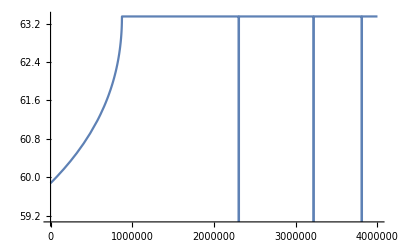

```mathematica
Plot[ϕsr[t],{t,0,4*10^6}]
```